## H_5^+ DVR — Outer H_2

5/9/2018

## Outer DVRs

```mathematica
Get@"~/Documents/UW/Research/H5+/Common/H5Core.m"
```

### Single H2 Test

#### Pre potential change

##### Energies

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR["Energies", "NumberOfWavefunctions"->10]
```

{3613.63,7152.95,10604.7,13874.9,16893.6,19817.3,22599.7,25266.6,27859.4}

##### Plots

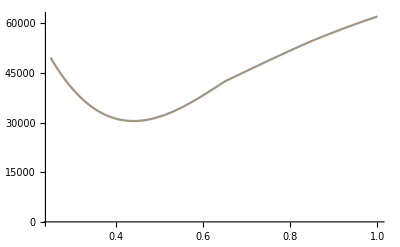

```mathematica
ListLinePlot[
$H2SingleDVR["GridPotentialEnergy"],
ColorFunction->"M10DefaultDensityGradient"
]
```

```mathematica
$H2SingleDVR[]
```

#### Post potential change

##### Energies

```mathematica
potMin=NMinimize[h2SinglePot[r], {r}∈Interval[{.25, 1}]]
```

{-521.157,{r→0.446384}}

```mathematica
$H2SingleDVR["Energies", "NumberOfWavefunctions"->10]
```

{1211.43,4642.61,8035.54,11412.3,14747.9,17921.1,20890.2,23779.,26531.4,29238.4}

```mathematica
$H2SingleDVR["Energies", "NumberOfWavefunctions"->10]-potMin[[1]]
```

{1732.59,5163.77,8556.69,11933.5,15269.,18442.3,21411.3,24300.1,27052.6,29759.6}

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR["Energies", "NumberOfWavefunctions"->10]
```

{3431.18,6824.11,10200.9,13536.5,16709.7,19678.7,22567.5,25320.,28027.}

Pot plot

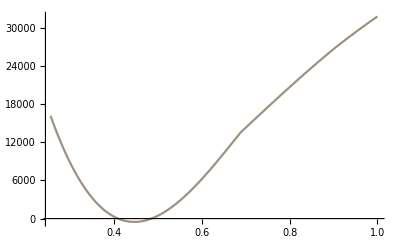

```mathematica
ListLinePlot[
$H2SingleDVR["GridPotentialEnergy"],
ColorFunction->"M10DefaultDensityGradient"
]
```

#### Potential Optimized DVR

##### Harmonic Potential

```mathematica
potFun=
{
"HarmonicOscillator",
"EquilibriumBondLength"->.65,
"ForceConstant"->10^8
};
```

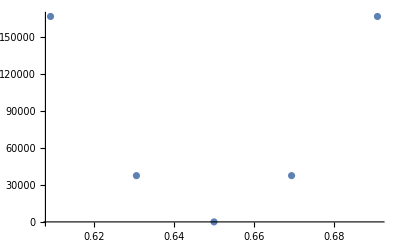

```mathematica
po=
$H2SingleDVR[
"PotentialOptimization", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->5,
"PotentialFunction"->potFun
];
poGrid=po[["Grid", 1]];
ListPlot[
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid,
"PotentialFunction"->potFun
]
]
```

```mathematica
eTrue=
Sort@$H2SingleDVR[
"Energies", 
"PotentialFunction"->potFun, 
"NumberOfWavefunctions"->10
]
```

{40898.3,122695.,204492.,286288.,368085.,449882.,531678.,613475.,695272.,777068.}

```mathematica
$H2SingleDVR[
"Energies",
"Grid"->po[["Grid", 1]],
"KineticEnergy"->po[["KineticEnergy", 1]],
"PotentialEnergy"->po[["PotentialEnergy", 1]]
]
```

{40898.3,122695.,204492.}

##### Proper Potential

```mathematica
potE2=
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid2,
"PotentialFunction"->h2SinglePot
];
```

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->6,
"PotentialFunction"->h2SinglePot,
"PotentialOptimize"->True,
"NumberOfWavefunctions"->All
]
```

```mathematica
{3613.014021283663,7142.091268658121,10385.833659392716,11928.765782050948,15564.83478532642}//Iconize
```

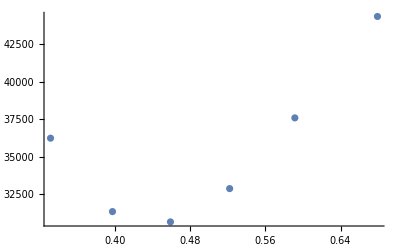

```mathematica
po2=
$H2SingleDVR[
"PotentialOptimization", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->6,
"PotentialFunction"->h2SinglePot
];
poGrid2=po2[["Grid", 1]];
ListPlot[
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid2,
"PotentialFunction"->h2SinglePot
]
]
```

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies",
"Points"->250,
"PotentialFunction"->h2SinglePot,
"NumberOfWavefunctions"->10
]
```

{3613.63,7152.95,10604.7,13874.9,16893.6,19817.3,22599.7,25266.6,27859.4}

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies",
"PotentialOptimize"->True,
"NumberOfWavefunctions"->10
]//AbsoluteTiming
```

{0.476663,{3613.64,7152.99,10604.9,13875.4,16893.7,19817.5,22599.8,25266.9,27859.4}}

### Double H2 PODVR

#### Plots

##### Proper Solutions

```mathematica
$H2DVR[ 
"PruningEnergy"->Scaled[.35],
"Points"->{30, 30},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"NumberOfWavefunctions"->5
]
```

```mathematica
$H2DVR[ 
"Wavefunctions",
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"NumberOfWavefunctions"->5
]//AbsoluteTiming
```

```mathematica
Rest[#]-First[#]&@
$H2DVR[ 
"Energies",
"Points"->{250, 250},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->50
},
"NumberOfWavefunctions"->6
]
```

{3495.56,3614.24,6938.68,7016.18,7191.27}

```mathematica
Iconize[
$H2DVR[ 
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PlotMode"->"Density",
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->8,
Boxed->False,
Axes->False,
ImageSize->300,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
"WavefunctionClipping"->None
]
]
```

```mathematica
Iconize[gpe]
```

```mathematica
gpe=
$H2DVR[ 
"GridPotentialEnergy",
"Points"->{80, 80}
];
```

```mathematica
$H2DVR[ 
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->6,
Boxed->False,
Axes->False,
ImageSize->300
];
```

##### Plots in the coupled potential

```mathematica
ListPlot3D[
$H2DVR[
"GridPotentialEnergy",
"Points"->{50, 50}
],
ColorFunction->h2ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

##### Plots in the uncoupled potential

```mathematica
ListPlot3D[
$H2DVR[
"GridPotentialEnergy",
"Points"->{250, 250},
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimize"->True,
"OptimizedBasisSize"->10
],
ColorFunction->h2ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

##### Frequencies from the coupled potential

```mathematica
$H2DVR[
"Energies",
"Points"->{60, 60},
"NumberOfWavefunctions"->10
]
```

{14712.8,18206.6,18325.4,21643.5,21719.4,21898.9,24978.8,25005.1,25214.7,25421.}

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"NumberOfWavefunctions"->10
]
```

{3493.75,3612.53,6930.62,7006.59,7186.11,10265.9,10292.3,10501.9,10708.2}

```mathematica
$H2DVR[
"Points"->{60, 60},
"NumberOfWavefunctions"->10,
"PlotDisplayMode"->List
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

##### Frequencies from the uncoupled potential

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"PotentialFunction"->{h2SinglePot,h2SinglePot}
]
```

{3610.51,3610.51,7136.94,7136.94,7221.03,10559.3,10559.3,10747.5,10747.5,13791.2,13791.2,14169.8,14169.8,14273.9,16772.4,16772.4,17401.7,17401.7,17696.3,17696.3,19656.3,19656.3,20382.9,20382.9}

##### PODVR

Plots

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{3494.82,3613.54,6935.31,7012.12}

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{3612.41,3612.41,7146.66,7224.82}

```mathematica
$H2DVR[
"Points"->{125, 125},
"ShowPotential"->False,
"ShowEnergies"->True,
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Test Energies

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->50
},
"NumberOfWavefunctions"->10
]
```

{3493.75,3612.53,6930.59,7006.54,7186.09,10265.7,10292.1,10501.8,10708.1}

Frequencies

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{250, 250},
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimize"->True,
"OptimizedBasisSize"->10,
"NumberOfWavefunctions"->10
]
```

{3613.63,3613.63,7152.95,7152.95,7227.27,10604.7,10604.7,10766.6,10766.6}

##### Extra Potentials

```mathematica
engs=
$H2DVR[
"Energies",
"Points"->{125, 125},
"PotentialEnergyOptions"->{
"PotentialFunction"->#
},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25,
"PotentialFunction"->{h2SinglePot,h2SinglePot}
},
"NumberOfWavefunctions"->12,
"ArnoldiIterations"->2500
]&/@h2Pots;
```

```mathematica
conts=
ListContourPlot[
$H2DVR[
"GridPotentialEnergy",
"Points"->{125, 125},
"PotentialEnergyOptions"->{
"PotentialFunction"->#
}
],
 ColorFunction->(Opacity[0]&), 
ContourStyle->GrayLevel[0, .35], 
PlotRangePadding->None
]&/@h2Pots;
```

```mathematica
wfnsies=
$H2DVR[
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialEnergyOptions"->{
"PotentialFunction"->#
},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25,
"PotentialFunction"->{h2SinglePot,h2SinglePot}
},
"NumberOfWavefunctions"->12,
"PlotMode"->"Density",
"ViewOptions"->
{
ColorFunctionScaling->True,
ColorFunction->ColorData@"Rainbow",
"ShowPotential"->False,
"WavefunctionClipping"->None
}
]&/@h2Pots;
```

```mathematica
plottos=
MapThread[
With[{cont=#},
MapThread[
Column@
{
Show[#, 
cont,
 PlotRangePadding->None,
 FrameTicks->None,
ImageSize->200
],
#2,
#3
}&,
{
#2,
#3,
#3-First[#3]
}
]
]&,
{
conts,
wfnsies,
engies-Min[engies]
}
];
```

```mathematica
plottoGrid=
Style[
KeyValueMap[
Prepend[#2, Grid@{{"R_1=", #[[1]]}, {"R_2=", #[[2]]}}]&,
plottos
]//Grid[#, ItemSize->Full]&,
FontFamily->"CMU Serif",
FontSize->24
]/.g_Grid:>Insert[g, Alignment->Center, 2];
```

```mathematica
biggyIm=
Rasterize[
plottoGrid,
ImageSize->2000
];
```

```mathematica
Export["~/Desktop/big_H2_R1_R2_effects.png", biggyIm]
```

~/Desktop/big_H2_R1_R2_effects.png

### Guess Wavefunctions DVR

```mathematica
$H2DVR["Range"]
```

{{-10.,10.},{-10.,10.}}

```mathematica
wfs=
Quiet@
$H2DVR["GuessWavefunctions", 
"PotentialFunction"->{h2SinglePot, h2SinglePot},
"UncoupledPotentialFunctions"->{h2SinglePot, h2SinglePot},
"GuessWavefunctionsComponents"->"Wavefunctions",
"NumberOfCombinations"->25
];
wfs[[1]]=wfs[[1, All, 1]]
```

{2422.11,5849.96,5849.96,9230.31,9230.31,9277.81,12580.6,12580.6,12658.2,12658.2,15881.7,15881.7,16008.5,16008.5,16038.5,19026.,19026.,19309.5,19309.5,19388.8,19388.8,21969.6,21969.6,22453.8,22453.8}

```mathematica
ChemTools["Get", "DVR/Package/GuessWavefunctions"]
```

```mathematica
$H2DVR[
"PotentialFunction"->None,
"UncoupledPotentialFunctions"->{h2SinglePot, h2SinglePot},
"GuessWavefunctionsComponents"->"Wavefunctions",
"NumberOfCombinations"->25,
"UseGuessWavefunctions"->True,
"ShowPotential"->False
]
```

ChemTools::DVRRun: Potential function Automatic didn't return a numerical vector over the gridpoints

Failure[…]